```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

LinkObject::linkw: Unable to write data to closed link ….

General::stop: Further output of LinkObject::linkw will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.1/Executables/wolfram -subkernel -noinit -nopaclet -wstp,184,9].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.1/Executables/wolfram -subkernel -noinit -nopaclet -wstp,186,11].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.1/Executables/wolfram -subkernel -noinit -nopaclet -wstp,187,12].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 11 of 14 kernels failed to initialize.

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import["../a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import["../LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import["../LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

(*activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];*)
activeLEC=LECsUNITmartinrimas[[All,{1,2,3}]];
```

```mathematica
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=3 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]

dimerCores={{2.00,{{3.49894,20.5763},{1.31002,2.03082},{0.230922,56.5742},{0.136023,20.549},{0.146917,20.5961}}}};
λRange=Range[1,Length[activeLEC]];
```

ℏ^2/(2  μ) = 13.8237

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
NormTF[core_?ArrayQ]:=1/Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^6/27)(1/((core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^6,{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta1,eta2,eta3,w1,w2,w3},
eta2= 3^(7/2)Cc /(((Aa+Bb)(Gg+Hh)(2 lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2 lam+3Gg+3Hh)))^(3/2));
w2= 3(Aa+Bb)(Gg+Hh)lam/(2lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2lam+3Gg+3Hh));
eta3 =3^(7/2)Dd /(((Aa+Bb)(lam+Gg+Hh)(lam Bb+Gg(4lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh)))^(3/2));
w3 = 6(Aa+Bb)(Gg+Hh)lam/(lam Bb+Gg(4 lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh));
eta1 =3^(7/2)Dd /(((Gg+Hh)(4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))))^(3/2));
w1=(3(Aa+Bb)lam(Aa+Bb+2lam)(Gg+Hh))/((4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta1 Exp[-w1 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=0;
a1=4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh;
b1=2Gg Bb -Gg Hh -2 Aa Bb +2 Aa Hh;
c1=Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh;

zeta2=0;
zeta3=0;

a2=4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh);
b2=Gg(4lam+2Bb-2 Hh)+Aa(-4lam-2Bb+2Gg);
c2=Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh);

a3= 4Bb(2lam+Hh)+Gg(Aa+2lam+Hh)+Aa(2lam+Bb+Hh);
b3=Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb);
c3=Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh);

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1;

Wmatt=ParallelTable[
cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;
DiagonalMatrix[Table[-cij hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]]
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmatt,4];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
(*Print[(Chop[Wmat])[[1;;4,1;;4]]//MatrixForm];*)
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
(*Print["N_terms = ",Length[a00]^4," calculated for E_rel = ",energyMeV," MeV"];*)
tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_]:=Module[{locall=l},

dataS={};
tanDsL={};
tanDs={};

eRange=Range[0.01,0.1,0.03];

LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];

SetSharedVariable[tanDs];

Do[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
,{energ,eRange[[1]]}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)

(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 eRange],Sqrt[mh2 eRange ]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦1;;3⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
{a0tf,r0tf,dataS}
]
```

```mathematica
JacobiTrailWavefunctionPara={{3.765815,7.217888,5.497260},{-1.031541222,7.217888,0.122223},{-0.81558642365,1.497478,0.122223},{-0.26860177627,0.124999,0.122223},{0.38054820786,11.420429,0.077848},{1.5081514531,4.030632,0.077848},{1.7809899176,0.741144,0.249935}};
Rmax=3;
grdPoints=50;
r1r2Range=Subdivide[Rmax,grdPoints-1];
JacobiTrailWavefunction=Total[#[[1]] Exp[-#[[2]] r1^2]Exp[-#[[3]] r2^2]&/@JacobiTrailWavefunctionPara];
JacobiTrailWavefunctionData=Table[JacobiTrailWavefunction/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobiTrailWavefunctionDataF=Flatten[Table[{R1,R2,JacobiTrailWavefunction/.{r1->R1,r2->R2}},{R1,r1r2Range},{R2,r1r2Range}],1];
```

```mathematica
FitCoreToGauss[nGauss_,core_,ami_:-10,ama_:10,bmi_:0.0,bma_:10]:=Module[{nk,amin,amax,bmin,bmax},
nk=nGauss;
amin=ami;amax=ama;
bmin=bmi;bmax=bma;
modelCluster={Sum[aLn@i Exp[-bLn@i (1./4. rrel1^2+1./3. rrel2^2)],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[core,modelCluster,Flatten[Table[{{aLn@i,RandomReal[{0.1 amin,0.2 amax}]},{bLn@i,RandomReal[{bmin,bmax}]}},{i,nk}],1],{rrel1,rrel2}(*,Weights->((#+1)^1&/@data[[All,1]])*)];
nlresi=nlmLABC["FitResiduals"];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
basispara
]
```

Heureka! a_(trimer - trimer) = 1.10999{{-11.3838,21.4255},{1.32472,2.0466},{51.1266,21.4256},{-35.7799,21.4255}}

Heureka! a_(trimer - trimer) = 0.956918{{-47.7945,2.52334},{49.0602,2.50581},{-3.04183,20.9801},{7.0529,20.98}}

Heureka! a_(trimer - trimer) = 0.957212{{27.2481,2.49829},{-58.2678,20.9763},{62.2787,20.9766},{-25.9823,2.53014}}

Heureka! a_(trimer - trimer) = 1.10999{{10.9176,21.4274},{-5.25977,21.4274},{1.32472,2.04661},{-1.69491,21.4274}}

Heureka! a_(trimer - trimer) = 1.1286{{1.31526,2.03572},{-36.9665,27.5209},{30.5864,25.4009},{10.3892,31.895}}

Heureka! a_(trimer - trimer) = 1.11003{{1.3247,2.04658},{-7.61437,21.4309},{-24.6017,21.4305},{36.179,21.4302}}

Heureka! a_(trimer - trimer) = 1.11007{{1.32468,2.04656},{-7.32417,21.357},{19.4907,21.3677},{-8.20369,21.3489}}

Heureka! a_(trimer - trimer) = 0.769934{{3.58859,23.319},{11.68,3.06324},{-17.9206,3.70368},{7.9618,4.69128}}

Heureka! a_(trimer - trimer) = 1.10999{{25.0322,21.4267},{1.32472,2.04661},{-10.4013,21.4266},{-10.6681,21.4266}}

Heureka! a_(trimer - trimer) = 1.12856{{22.8401,25.2146},{1.31529,2.03574},{25.2247,30.7833},{-44.0558,28.6337}}

Heureka! a_(trimer - trimer) = 1.12841{{39.1799,25.809},{1.31539,2.03584},{-62.8053,28.0521},{27.6343,30.4531}}

Heureka! a_(trimer - trimer) = 1.12855{{16.7435,31.1522},{1.31529,2.03575},{-40.9033,28.0304},{28.1689,25.4133}}

Heureka! a_(trimer - trimer) = 0.762632{{22.199,3.2201},{-37.3408,3.69098},{16.8485,4.32758},{3.60279,23.2655}}

Heureka! a_(trimer - trimer) = 0.759199{{34.639,4.113},{3.60923,23.241},{42.2154,3.33911},{-75.1543,3.68499}}

Heureka! a_(trimer - trimer) = 1.12859{{1.31526,2.03572},{-37.1781,28.2924},{17.4571,31.1718},{23.73,25.226}}

Heureka! a_(trimer - trimer) = 0.956983{{25.0065,2.49733},{-9.11321,2.5322},{4.01105,20.98},{-14.6276,2.53214}}

Heureka! a_(trimer - trimer) = -4.54834×10^-6{{19.0317,1.85358},{4.0128,20.7878},{-17.7515,1.85358},{-0.0235423,6.06771×10^-6}}

Heureka! a_(trimer - trimer) = 1.1286{{1.31527,2.03572},{13.0496,31.4664},{-41.9641,27.6361},{32.9235,25.5142}}

Heureka! a_(trimer - trimer) = 1.12625{{37.7216,25.9923},{16.7258,31.6488},{1.3167,2.03716},{-50.4383,28.1245}}

Heureka! a_(trimer - trimer) = 0.771848{{6.99568,4.77693},{-15.7567,3.70692},{10.4861,3.03247},{3.58477,23.3334}}

Heureka! a_(trimer - trimer) = 1.10999{{60.3872,21.4264},{1.32472,2.04661},{-28.191,21.4263},{-28.2333,21.4263}}

Heureka! a_(trimer - trimer) = 1.12876{{15.7078,24.6518},{15.668,31.6074},{-27.3665,28.9226},{1.31515,2.03562}}

Heureka! a_(trimer - trimer) = 1.12908{{5.21633,33.7007},{13.791,24.2944},{1.31492,2.03541},{-14.9979,27.9969}}

Heureka! a_(trimer - trimer) = 1.11004{{-48.9632,21.4097},{85.529,21.4109},{-32.603,21.4107},{1.3247,2.04658}}

Heureka! a_(trimer - trimer) = 1.12898{{14.4624,24.4202},{6.96932,32.9879},{1.31499,2.03547},{-17.4224,28.2477}}

Heureka! a_(trimer - trimer) = 1.14092{{21.5277,22.2649},{3.08471,28.7564},{1.3072,2.02801},{-20.6067,23.2675}}

Heureka! a_(trimer - trimer) = 0.956945{{2.86563,20.981},{1.14544,20.977},{27.9378,2.49919},{-26.6722,2.53029}}

Heureka! a_(trimer - trimer) = 0.78162{{7.08356,2.90815},{4.33915,5.18797},{3.56434,23.4088},{-9.67677,3.72361}}

Heureka! a_(trimer - trimer) = 2.34475{{23.2459,1.34361},{-24.1016,20.5129},{28.1409,20.5129},{-22.0233,1.31914}}

Heureka! a_(trimer - trimer) = 0.764723{{3.59853,23.2816},{18.4061,3.17432},{-28.6788,3.66993},{11.9837,4.46021}}

Heureka! a_(trimer - trimer) = 1.12978{{-6.84637,29.1797},{1.31441,2.03495},{3.11633,35.8336},{7.73988,23.1368}}

Heureka! a_(trimer - trimer) = 0.956968{{25.4893,2.49768},{11.0823,20.9792},{-7.07122,20.9788},{-24.2237,2.53184}}

Heureka! a_(trimer - trimer) = 0.771166{{9.18036,3.00864},{3.58735,23.3247},{10.1225,4.62184},{-17.5803,3.84703}}

Heureka! a_(trimer - trimer) = 0.814336{{5.24065,2.73579},{3.39222,24.0261},{-4.82258,3.37729},{1.50305,7.60978}}

Heureka! a_(trimer - trimer) = 0.770719{{11.158,3.05036},{7.53697,4.7265},{3.58704,23.3248},{-16.9722,3.70497}}

Heureka! a_(trimer - trimer) = 0.758964{{45.1259,3.34963},{3.60966,23.2393},{-80.7035,3.68459},{37.2772,4.096}}

Heureka! a_(trimer - trimer) = 0.957015{{19.6605,2.49262},{-11.606,20.9802},{-18.3948,2.53725},{15.617,20.9801}}

Heureka! a_(trimer - trimer) = 1.1292{{34.2841,24.9856},{-33.5421,26.2222},{1.31484,2.03534},{3.26736,34.8498}}

Heureka! a_(trimer - trimer) = 1.10998{{24.2563,21.4276},{-15.477,21.4276},{-4.81637,21.4276},{1.32472,2.04661}}

Heureka! a_(trimer - trimer) = 0.766585{{7.61237,4.67651},{3.5908,23.3125},{-24.8035,3.57177},{18.9101,3.15809}}

Heureka! a_(trimer - trimer) = 0.759637{{3.60841,23.2441},{37.685,3.32046},{30.5565,4.14384},{-66.5406,3.68577}}

Heureka! a_(trimer - trimer) = 1.13264{{4.11428,21.1131},{-4.40134,40.3738},{1.31236,2.0331},{4.29954,42.3608}}

Heureka! a_(trimer - trimer) = 1.13264{{9.94555,23.3137},{1.31267,2.0332},{3.72553,33.4852},{-9.66212,27.5582}}

Heureka! a_(trimer - trimer) = 2.34243{{46.0864,1.33756},{-44.8637,1.32539},{-4.63619,20.5132},{8.67547,20.5132}}

Heureka! a_(trimer - trimer) = 1.12901{{-16.7353,28.2601},{1.31497,2.03545},{14.06,24.3695},{6.68464,33.0969}}

Heureka! a_(trimer - trimer) = 1.10999{{18.7581,21.4274},{1.32472,2.04661},{-2.23597,21.4276},{-12.5593,21.4273}}

Heureka! a_(trimer - trimer) = 0.769549{{7.36087,4.71839},{3.58901,23.3164},{13.2866,3.08852},{-18.9268,3.64641}}

Heureka! a_(trimer - trimer) = 0.76042{{31.7457,3.29045},{-55.2862,3.68713},{25.243,4.19554},{3.60695,23.2497}}

Heureka! a_(trimer - trimer) = 0.774529{{5.98162,4.89332},{-13.4626,3.7115},{3.57932,23.3536},{9.21165,2.99362}}

Heureka! a_(trimer - trimer) = 2.25304{{-7.16682,1.30011},{8.39238,1.37146},{4.80319,20.8876},{-0.766162,22.8293}}

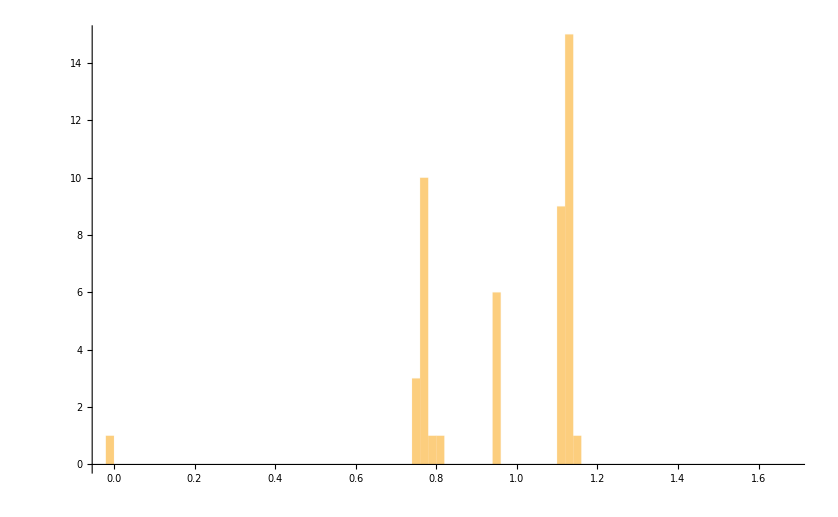

```mathematica
results={};
fitDim=4;
rMax=20;
nGrd=100;
nIter=50;
Do[
tmpCore=FitCoreToGauss[fitDim,JacobiTrailWavefunctionDataF,RandomReal[{-100,0}],RandomReal[{100,1000}],0,RandomReal[{30,60}]];

tmp=GetERE[2,rMax,nGrd,tmpCore];

AppendTo[results,tmp[[1]]];
Print["Heureka! a_(trimer - trimer) = ",results[[-1]],tmpCore]
,{nn,Range[nIter]}]
Histogram[results,{0.02}]
```